# NEAT

студент 3 курса 5 группы
Лицкевич Данила
20-12-2020

# NEAT

## 0. Info

https://towardsdatascience.com/neat-an-awesome-approach-to-neuroevolution-3eca5cc7930f

## Generating individual old

Гаплоидный генотип. Фазовое пространство данной задачи состоит из особей, характеризующихся одиннадцатью признаками {α_i}∈ℝ^11, каждый из которых задаёт некий угол в градусах. 
α_1 — угол наклона головы, изменяется в пределах -90°⩽α_1⩽+90 °;
α_2 — угол наклона корпуса, изменяется в пределах -45°⩽α_2⩽+180 °;

Точность α_1:Δx <1° ⟹ Y > 180° ⟹ bits > 8       Δx ≈0.703125

### Nodes

Input and output nodes are not evolved in the node gene list. Hidden nodes can be added or removed.

Input — количество входов - fixed;
Output — количество выходов - fixed;
Hidden — количество скрытых нейронов - 0 ≤ Hidden ≤ Total-Input-Output;
Total — количество нейронов - 0 ≤ Total ≤ 255;

Точность Total:Δx =1  ⟹ bits = 8

```mathematica
Nodes[in_,out_,hidden_]:=Flatten[{ConstantArray["I",in],ConstantArray["O",out],ConstantArray["H",hidden]}]
```

### Connections

Input — нейрон входа - 0 ≤ Total ≤ 255;
Output — нейрон выхода - 0 ≤ Total ≤ 255;
weight — количество скрытых нейронов -90 ≤ weight ≤ +90 ;
enabled — активирована ли связь - 0 ≤ enabled ≤ 1;
inovation — активирована ли связь - 0 ≤ enabled ≤ 1;

Точность Input:Δx =1  ⟹ bits = 8       
Точность Output:Δx =1  ⟹ bits = 8       
Точность weight:Δx <0.1  ⟹ bits = 11     ⟹   Δx =180/2048≂0.0878906

Точность α_1:Δx <1° ⟹ Y > 180° ⟹ bits > 8       Δx ≈0.703125

Точность Total:Δx =1 ⟹ Y > 180° ⟹ bits = 8

Точность Total:Δx =1 ⟹ Y > 180° ⟹ bits = 8

```mathematica
Connection[in_,out_,weight_,enabled_,inovation_]={}
```

## 1. Individuals

## Generating Population

### Connections

#### kmConnection

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
kmConnection[in_,out_,weight_,enabled_,inovation_]:=<|
"input"->in,
"output"->out,
"weight"->weight,
"enabled"->enabled,
"inovation"->inovation
|>
```

### Individual

Input and output nodes are not evolved in the node gene list. Hidden nodes can be added or removed.

Total — количество всех нейронов;

```mathematica
ClearAll[kmAddIndividual]
SetAttributes[kmAddIndividual,HoldFirst]
kmAddIndividual[population_,hidden_:0]:=
AppendTo[population["individuals"],
<|
"input"->population["input"],
"output"->population["output"],
"total"->population["input"]+population["output"]+hidden,
"connections"->(kmNewConnection[population,#]&/@
With[
{},
Flatten[
Outer[
{#1,#2}&,
Range[population["input"]],
Range[population["input"]+1,population["input"]+population["output"]]
],1]
])
|>]
```

### Inovations

#### kmInovation

```mathematica
kmInovation[in_,out_,inovation_]:=<|
"input"->in,
"output"->out,
"inovation"->inovation
|>
```

### Population

Input — количество входов;
Output — количество выходов;

```mathematica
kmPopulation[in_,out_,options___]:=<|
"input"->in,
"output"->out,
"best"-><||>,
"inovations"->{},
"individuals"->{}
|>
```

### Connection' s logics

#### kmDetermineInovation

Return Inovation id
(if new Inovation then appends to others)

```mathematica
SetAttributes[kmDetermineInovation,HoldFirst]
kmDetermineInovation[population_,in_,out_]:=Catch[
Scan[
If[in===#["input"]&&out===#["output"],Throw[#["inovation"]]]&,
population["inovations"]
];
With[{newInovation=Length[population["inovations"]]+1},
AppendTo[population["inovations"],kmInovation[in,out,newInovation]];
Throw[newInovation]
]
]
```

#### kmNewConnection

```mathematica
ClearAll[kmNewConnection]
SetAttributes[kmNewConnection,HoldFirst]
kmNewConnection[population_,{in_,out_},enabledRate_:0.95,options___]:=
kmConnection[in,out,RandomReal[{-1,1}],RandomReal[]<enabledRate,kmDetermineInovation[population,in,out]]
```

#### kmNotInNodesTree

Finds all nodes which cannot be as IN nodes for a node

```mathematica
kmInNodesTree[history_,out_]:=Block[
{inNodes={out}},
If[Or@@ Thread@Equal[inNodes,#["output"]],AppendTo[inNodes,#["input"]]]&/@history;
inNodes
]
```

#### kmValidConnectionQ

```mathematica
kmValidConnectionQ[population_,{in_,out_}]:= 
And[out>population["input"],out≤population["input"],out>population["output"],
And@@Thread@Unequal[kmInNodesTree[population["inovations"],out],in]]
```

```mathematica
kmValidConnectionQ[testPop,{4,3}]
```

True

```mathematica
kmInNodesTree[testPop["inovations"],3]
```

{3,1,2,6}

#### kmAddNode

```mathematica
SetAttributes[kmAddNode,HoldFirst]
kmAddNode[population_,individualId_,connectionId_]:= 
Block[{
individual=population["individuals"]⟦individualId⟧,
connection
},
connection=individual["connections"]⟦connectionId⟧;
individual⟦"connections",connectionId,"enabled"⟧=False;
individual⟦"total"⟧+=1;
individual⟦"connections"⟧=Join[
{kmNewConnection[population,{connection["input"],#},1],
kmNewConnection[population,{#,connection["output"]},1]}&[individual["total"]],
individual["connections"]
];
population⟦"individuals", individualId⟧=individual
]
```

```mathematica
kmAddNode[testPop,1,1]
```

<|input→2,output→3,total→6,connections→{<|input→1,output→6,weight→-0.932167,enabled→True,inovation→7|>,<|input→6,output→3,weight→0.633751,enabled→True,inovation→8|>,<|input→1,output→3,weight→-0.387425,enabled→False,inovation→1|>,<|input→1,output→4,weight→-0.102258,enabled→True,inovation→2|>,<|input→1,output→5,weight→0.473294,enabled→True,inovation→3|>,<|input→2,output→3,weight→-0.444066,enabled→True,inovation→4|>,<|input→2,output→4,weight→0.536706,enabled→True,inovation→5|>,<|input→2,output→5,weight→0.982851,enabled→True,inovation→6|>}|>

### Tests

```mathematica
testPop=kmPopulation[2,3]
```

<|input→2,output→3,best→<||>,inovations→{},individuals→{}|>

```mathematica
kmAddIndividual[testPop]
```

{<|input→2,output→3,total→5,connections→{<|input→1,output→3,weight→-0.387425,enabled→True,inovation→1|>,<|input→1,output→4,weight→-0.102258,enabled→True,inovation→2|>,<|input→1,output→5,weight→0.473294,enabled→True,inovation→3|>,<|input→2,output→3,weight→-0.444066,enabled→True,inovation→4|>,<|input→2,output→4,weight→0.536706,enabled→True,inovation→5|>,<|input→2,output→5,weight→0.982851,enabled→True,inovation→6|>}|>}

```mathematica
Dynamic@testPop
```

## Population viewing (realisatoin Delayed)

```mathematica
testIndividual=<|"input"->2,"output"->3,"hidden"->4,"connections"->{<|"input"->1,"output"->5,"weight"->-0.9628618224751473,"enabled"->1,"inovation"->1|>,<|"input"->3,"output"->4,"weight"->0.22393191857363837,"enabled"->1,"inovation"->2|>,<|"input"->4,"output"->6,"weight"->-0.4785485230617863,"enabled"->1,"inovation"->3|>,<|"input"->6,"output"->5,"weight"->0.45075859641862426,"enabled"->1,"inovation"->4|>,<|"input"->8,"output"->5,"weight"->0.5039873848534051,"enabled"->1,"inovation"->5|>}|>;
```

### Individual viewing

#### kmNodes

1  – in node
2  – out node
3  – hidden node

```mathematica
kmNodes[type_,nodesQuant_,level_]:=
{Switch[type,1,Red,2,Blue,3,Gray,True,Black],Disk[{-nodesQuant+2#,level},0.25]&/@Range[nodesQuant]}
```

#### kmViewIndividual

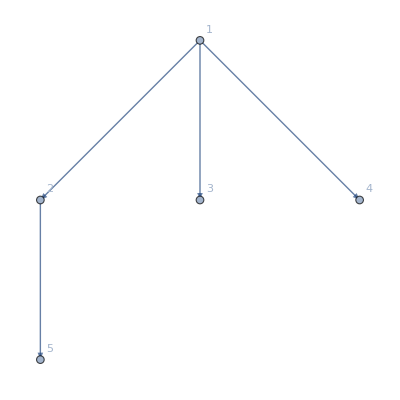

```mathematica
TreeGraph[{1->2,1->3,1->4,2->5},EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow",VertexLabels->"Name"]
```

```mathematica
kmViewIndividual[individ_]:=
Graphics[{kmNodes[1,3,1],kmNodes[2,2,2]}]
```

```mathematica
Dynamic@kmViewIndividual[1]
```

```mathematica
Graph
```

### Population viewing

## Population mutations